# Universal Estimator

## Parameter range adjustment

For convenience, we want to work with parameters  ∈ (0,1) and map them to the parameters in the original range.
For that, we can use the Logistic function and its Logit inverse.

#### The Logistic function

The standard Logistic function, σ(x), defined in (-∞, ∞) and yields values in (0,1):

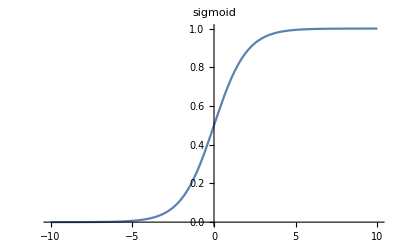

```mathematica
Sigmoid[x_]:=1/(1+ⅇ^-x)
Plot[Sigmoid[x], {x, -10, +10}, PlotLabel->HoldForm[sigmoid]]
```

#### The Logit function

The Logit  is the inverse of the Logistic function σ(x), defined in (0,1) and yields values in (-∞, ∞).
Let’s find the inverse:
σ(x) = y =  1/(1+e^-x) ⇒  1+e^-x = 1/y  ⇒  e^-x = 1/y-1=(1-y)/y  ⇒  log(e^-x)=log((1-y)/y)  ⇒  -x = log((1-y)/y)  ⇒  x = log(y/(1-y)) = σ^-1(x)

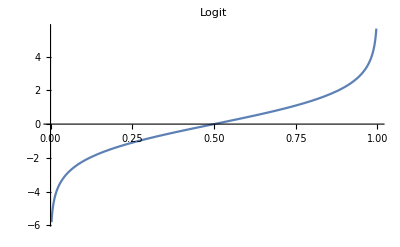

```mathematica
Logit[x_]:= Log[x/(1-x)]
Plot[Logit[x], {x, 0, 1}, PlotLabel->HoldForm[Logit]]
```

### Range Adjuster

We define an Adjuster function which returns another function that maps a parameter in the range  (0,1) to the range  (low, high) of the original distribution.
We can use the Logistic function and its Logit inverse as follows:
Let
	h(t) = Logit(t) , t ∈ (0,1)
Than
	h^-1(d) = Sigmoid(d) , d ∈ (-∞, ∞)

```mathematica
Adjuster[low_, high_]:=With[{LOW=Sigmoid[low],HIGH=Sigmoid[high]}, Function[{t},Logit[LOW+t(HIGH-LOW)]]]
```

### Test Adjuster

For example, we can create an Adjuster for the range [2,5] and call it with values ∈ [0,1]

```mathematica
adj=Adjuster[2, 5];
Print[adj[0.01]];
```

2.01076

```mathematica
Print[adj[0.99]];
```

4.84348

Plot of the adjuster output in the range [0,1]

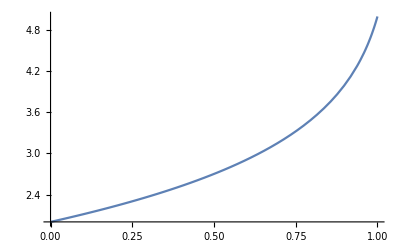

```mathematica
Print[Plot[adj[x], {x,0,1}]]
```

## Generate data

Arguments:

nSamples: number of samples

M: number of observations in each sample

f: the function to generate samples

ranges: an array [d X 2] of parameter ranges (e.g. for 2 parameters: [[0, 10], [0, ∞]])

bins: number of bins in histograms (default: max[samples]+1)

Returns:

samples, params, histograms

```mathematica
GenerateData[nSamples_, M_, f_, ranges_, bins_:-1]:= 
Module[{nParams, adjusters, params, samples, nbins, histograms},

(*number of parameters*)
nParams=Dimensions[ranges][[1]];

(*generate an adapter for each parameter range*)
adjusters=Table[Adjuster[ranges[[i,1]],ranges[[i,2]]],{i,1,nParams}];

(*generate N parameters cube in the range (0,1)*)
params=Table[adjusters[[j]][RandomReal[{0,1}]],{i,1,nSamples},{j,1,nParams}];

(*generate N samples from the parameters*)
samples=Table[f[params[[i]],M],{i,1,nSamples}];

(*create a histogram for each sample*)
nbins=If [bins>0,bins,Max[samples]+1];
h[x_]:=HistogramList[x, {0,nbins,1}][[2]];
histograms=Map[h,samples];

(*output*)
{params,samples, histograms}
]
```

Test GenerateData

```mathematica
YuleSimon[{alpha_,beta_}, size_]:=RandomVariate[WaringYuleDistribution[alpha,beta],size];
ranges = {{2,3},{0,10}};

data = GenerateData[5,20,YuleSimon, ranges];

Print["params:"];
Print[data[[1]]// TableForm];
Print["samples:"];
Print[data[[2]]// TableForm];
Print["histograms:"];
Print[data[[3]]// TableForm];
```

params:

2.77748 | 0.545046
2.59361 | 2.82398
2.38385 | 0.706641
2.25868 | 2.95401
2.04233 | 0.745748

samples:

2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 5 | 1 | 5 | 0 | 1 | 3 | 0 | 0 | 8 | 3 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 4 | 5 | 3 | 0 | 0 | 0 | 1 | 3 | 0 | 2 | 0 | 3
0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11 | 0 | 0 | 1 | 0 | 0 | 0

histograms:

18 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11 | 3 | 0 | 2 | 0 | 2 | 0 | 0 | 2 | 0 | 0 | 0
16 | 3 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11 | 2 | 2 | 3 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
15 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1

```mathematica
?HistogramList
```

## Define DNN

```mathematica
M = 256
net = NetChain[{
LinearLayer[M], 
BatchNormalizationLayer[],
ElementwiseLayer[Ramp],
LinearLayer[M], 
BatchNormalizationLayer[],
ElementwiseLayer[Ramp],
LinearLayer[M], 
BatchNormalizationLayer[],
ElementwiseLayer[Ramp], 
LinearLayer[1]},
"Input"->M, 
"Output" -> "Scalar"]
```

256

NetChain[<>]

## Experiments

```mathematica
results = Import["/home/yossi/Documents/Wolfram Mathematica/cached_mesh_points.csv"];

(*dict["sample"] = YuleSimon
dict["ranges"] = {{2,3},{0,10}}
dict["M"] = 256
f = dict["sample"]
ranges = dict["ranges"]
f[ranges[[1,1]], dict["M"]]
*)
```